1. Naloga

a)

```mathematica
(1/3 + 1/6)^2
```

1/4

b)

```mathematica
3/(6/8)
```

4

c)

```mathematica
Sin[Pi/2]
```

1

d)

```mathematica
E^(Log[7])
```

7

2. Naloga

a)

```mathematica
Simplify[((3+4x)/(2+5x))^2+((2+x)/(1-x))^2]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

b)

```mathematica
Simplify[x/y+y/x+2]
```

(x+y)^2/(x y)

c)

```mathematica
Factor[(x^2+y^2)^2-2(xy)^2]
```

x^4-2 xy^2+2 x^2 y^2+y^4

d)

```mathematica
Simplify[(Sin[x])^2+(Cos[x])^2]
```

1

e)

```mathematica
Simplify[2Sin[x]Cos[x]]
```

Sin[2 x]

f)

```mathematica
FullSimplify[(Tan[Pi/8])^4+(Cot[Pi/8])^4]
```

34

g)

```mathematica
FullSimplify[Sqrt[278 +42Sqrt[5]-12Sqrt[6]-28Sqrt[30]] ]
```

3+7 √5-2 √6

3. Naloga

a)

```mathematica
Expand[(x+xy+y)^10]
```

x^10+10 x^9 xy+45 x^8 xy^2+120 x^7 xy^3+210 x^6 xy^4+252 x^5 xy^5+210 x^4 xy^6+120 x^3 xy^7+45 x^2 xy^8+10 x xy^9+xy^10+10 x^9 y+90 x^8 xy y+360 x^7 xy^2 y+840 x^6 xy^3 y+1260 x^5 xy^4 y+1260 x^4 xy^5 y+840 x^3 xy^6 y+360 x^2 xy^7 y+90 x xy^8 y+10 xy^9 y+45 x^8 y^2+360 x^7 xy y^2+1260 x^6 xy^2 y^2+2520 x^5 xy^3 y^2+3150 x^4 xy^4 y^2+2520 x^3 xy^5 y^2+1260 x^2 xy^6 y^2+360 x xy^7 y^2+45 xy^8 y^2+120 x^7 y^3+840 x^6 xy y^3+2520 x^5 xy^2 y^3+4200 x^4 xy^3 y^3+4200 x^3 xy^4 y^3+2520 x^2 xy^5 y^3+840 x xy^6 y^3+120 xy^7 y^3+210 x^6 y^4+1260 x^5 xy y^4+3150 x^4 xy^2 y^4+4200 x^3 xy^3 y^4+3150 x^2 xy^4 y^4+1260 x xy^5 y^4+210 xy^6 y^4+252 x^5 y^5+1260 x^4 xy y^5+2520 x^3 xy^2 y^5+2520 x^2 xy^3 y^5+1260 x xy^4 y^5+252 xy^5 y^5+210 x^4 y^6+840 x^3 xy y^6+1260 x^2 xy^2 y^6+840 x xy^3 y^6+210 xy^4 y^6+120 x^3 y^7+360 x^2 xy y^7+360 x xy^2 y^7+120 xy^3 y^7+45 x^2 y^8+90 x xy y^8+45 xy^2 y^8+10 x y^9+10 xy y^9+y^10

b)

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

4. Naloga

```mathematica
a=3
b=4
c=6
```

3

4

6

```mathematica
o=a+b+c
s=o/2
```

13

13/2

```mathematica
Sqrt[s(s-a)(s-b)(s-c)]
```

(√455)/4

Zgornji rezultat predstavlja ploščino trikotnika s stranicami a, b in c.

```mathematica
Clear[a,b,c,o,s]
```

5. Naloga

```mathematica
s={3,2,0,0,5,13,2,-x,8}
s[[5]]
s[[-1]]
```

{3,2,0,0,5,13,2,-x,8}

5

8

Ukaz vrne prvi element seznama v obratnem vrstnem redu.

6. Naloga

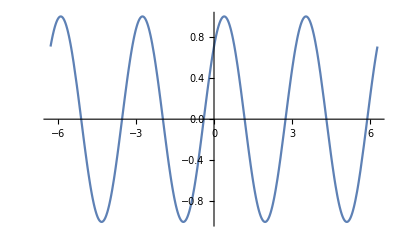

```mathematica
Plot[Sin[2x+Pi/4], {x,-2Pi, 2Pi}]
```

7. Naloga

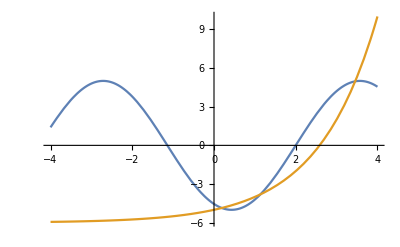

```mathematica
f[x_]:=5Sin[x-2]
g[x_]:=2^x-6
Plot[{f[x],g[x]}, {x, -4,4}]
```

8. Naloga

```mathematica
a=3^200+20
b=2^300+30
a==b
a<b
a>b
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044021

2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397406

False

False

True

Enakost ne drži. Prva neenakost ne drži, druga pa drži.

9. Naloga

```mathematica
Solve[x^2+4x+2==0, x]
Solve[x^2+4x+5==0, x]
```

{{x→-2-√2},{x→-2+√2}}

{{x→-2-ⅈ},{x→-2+ⅈ}}

Rešitvi druge enačbe sta kompleksni števili.

10. Naloga

```mathematica
Reduce[x^4==1, x]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

11. Naloga

a)

```mathematica
f[x_]:=(x^2-CubeRoot[x^2])*E^x
```

b)

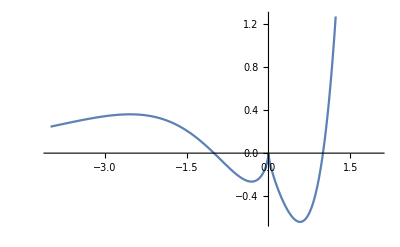

```mathematica
Plot[f[x], {x,-4,2}]
```

Iz grafa se da razbrati, da so ničle funkcije f (x) x1 = -1, x2 = 0 in x3 = 1.

c)

```mathematica
Solve[f[x]==0, x]
Reduce[f[x]==0, x]
```

{{x→-1},{x→0},{x→1}}

x==-1||x==0||x==1

Funkciji Solve in Reduce se razlikujeta le pri izpisu vrnjenega.